```mathematica
ω=1;
Subscript[k, 0]=1;
k=Subscript[k, 0]*4;
n=4*ω;
Subscript[ϕ, t]=ArcTan[n];
Subscript[ϕ, r]=(2*n)/(1-n*n);
Subscript[E, i]=1;
Subscript[E, r]=Subscript[E, i];
Subscript[E, t]=(2*Subscript[E, i])/Sqrt[n*n+1];
```

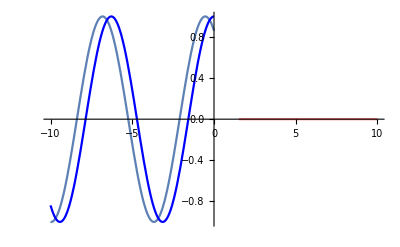

```mathematica
Show[Plot[Subscript[E, t]*Cos[Subscript[ϕ, t]]*Exp[-k*z],{z,0,10},PlotStyle->Pink],Plot[Subscript[E, r]*Cos[-Subscript[k, 0]*z+Subscript[ϕ, r]],{z,-10,0}],Plot[Subscript[E, i]*Cos[Subscript[k, 0]*z],{z,-10,0},PlotStyle->Blue],PlotRange->All]
```

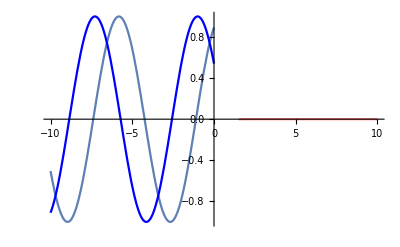

```mathematica
Show[Plot[Subscript[E, t]*Cos[1+Subscript[ϕ, t]]*Exp[-k*z],{z,0,10},PlotStyle->Pink],Plot[Subscript[E, r]*Cos[-Subscript[k, 0]*z+1+Subscript[ϕ, r]],{z,-10,0}],Plot[Subscript[E, i]*Cos[Subscript[k, 0]*z+1],{z,-10,0},PlotStyle->Blue],PlotRange->All]
```

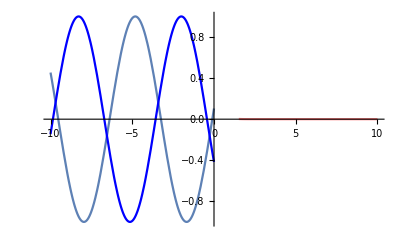

```mathematica
Show[Plot[Subscript[E, t]*Cos[Subscript[ϕ, t]]*Exp[-k*z+2],{z,0,10},PlotStyle->Pink],Plot[Subscript[E, r]*Cos[-Subscript[k, 0]*z+Subscript[ϕ, r]+2],{z,-10,0}],Plot[Subscript[E, i]*Cos[Subscript[k, 0]*z+2],{z,-10,0},PlotStyle->Blue],PlotRange->All]
```